```mathematica
Bode Plot program for an arbitrary frequency response
```

```mathematica
H (ⅉ ω)=(K ⅉω (ⅉω/Subscript[z, 1]+1)...(ⅉω/Subscript[z, n]+1))/(ⅉω (ⅉω/Subscript[p, 1]+1)... (ⅉω/Subscript[p, n]+1))
|H(ⅉω)|=20 Subscript[log, 10](K)+(∑_(i=1)^n 20 Subscript[log, 10]|1+ⅉω/Subscript[z, i]|)-(∑_(j=1)^m 20 Subscript[log, 10]|1+ⅉω/Subscript[p, j]|)
ϕ(ⅉω)=∑_(i=1)^n arctan(ω/Subscript[z, i])-∑_(j=1)^m arctan(ω/Subscript[p, j])
```

H(ⅉω)= 40/((1+(ⅈ ω)/50000) (1+(ⅈ ω)/10000) (1+(ⅈ ω)/600) (1+(ⅈ ω)/20))

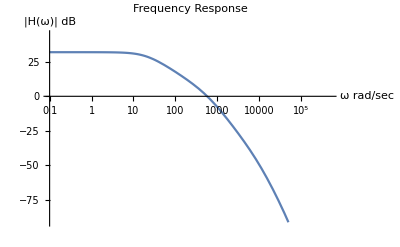

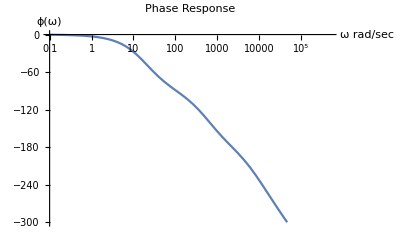

```mathematica
(*Start of Program*)
Clear["Global`*"]
K=Input["Enter The Value Of Gain"];
n = Input["Enter The Number Of Poles"];
listOfPoles =Table[Input["Enter The Value Of A Pole"],n];
listOfPhases=(1/#)&[listOfPoles];
H[ω_]:=K*Times@@(1/(1+(ⅉ*ω)/#))&[listOfPoles](*This makes the function ∏_(i=1)^n 1/(1+ⅉω/Subscript[p, i])*)
StringForm["H(ⅉω)= ``",H[ω]]
(*dB=20*Log[10,K]+(Plus@@-listOfTerms);*)
ϕ[ω_]:=Arg[K]+(Plus@@-(180/π*ArcTan[ω*#]&[listOfPhases]))
LogLinearPlot[20*Log[10,Abs[H[ω]]],{ω,0.1,10*Max[listOfPoles]},PlotRange->{{0.1,10*Max[listOfPoles]},{20*Log[10,Abs[H[Max[listOfPoles]]]],28*Log[10,K]}},PlotLabel->"Frequency Response", AxesLabel->{"ω rad/sec","|H(ω)| dB"}]
LogLinearPlot[ϕ[ω], {ω,0.1,10*Max[listOfPoles]},PlotRange->{{0.1,10*Max[listOfPoles]},{-300,0}},PlotLabel->"Phase Response", AxesLabel->{"ω rad/sec","ϕ(ω)"}]
```